Дзебан Арсений 0В21 вариант - 6

Вычислить собственные значения и функции задачи Штурма-Лиувилля. Построить таблицу содержащую первые 5 собственных чисел из собственных функций,изобразить их графически. Проверить ортогональность  любой пары собственных функций. Сделать выводы.
Исходное уравнение: y’’[x]+λ y[x]==0,y’[0]==0,y’[1]==0
Запишем общее решение с помощью Dsolve:

```mathematica
sol=DSolve[{y''[x]+λ y[x]==0,y'[0]==0,y'[1]==0},y[x],x]
```

{{y[x]→Piecewise[{{C[1] Cos[x √λ], n∈ℤ&&n≥0&&λ==n^2 π^2}, {0, True}}]}}

Для получения собственных функций в задаче Штурма-Лиувилля подставим λ:

```mathematica
eigfuns=Table[y[x]/. sol[[1]]//.{n->i,λ->(Pi*n)^2}/. {C[1]->1},{i,5}]
```

{Cos[π x],Cos[2 π x],Cos[3 π x],Cos[4 π x],Cos[5 π x]}

Зарисуем графики собственных функций на отрезке  [0;1]

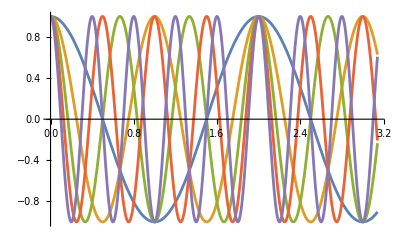

```mathematica
Plot[Evaluate[eigfuns],{x,0,Pi}]
```

Для проверки здесь и далее будем составлять матрицу попарных скалярных произведений в пространстве L2[0;1], тогда матрица для ортогонального конечного набора функций будет содержать нули на всех элементах, кроме 
диагональных:

Вычислим скалярные произведения по определению:

```mathematica
M=Table[Integrate[eigfuns[[i]]*eigfuns[[j]],{x,0,1}],{i,1,Length[eigfuns]},{j,1,Length[eigfuns]}];
```

```mathematica
M //MatrixForm
```

(1/2 | 0 | 0 | 0 | 0
0 | 1/2 | 0 | 0 | 0
0 | 0 | 1/2 | 0 | 0
0 | 0 | 0 | 1/2 | 0
0 | 0 | 0 | 0 | 1/2)

Вывод: поскольку описанное выше условие ортогональности некоторого набора собственных функций решения задачи Ш-Л ДУ выполнено, можно считать эти функции попарно ортогональными (что и является свойством решений Ш-Л ДУ, т. е решение получено верно). Ожидаемо, что при условиях Штурма 2-го рода ряд функций состоит из косинусов.

Задача 2: аналогична задаче 1, при этом
уравнение выглядит следующим образом: 
y2’’[x]+λ y2[x]==0,y2[0]- y2’[0]==0,y2[1]==0

```mathematica
sol2=DSolve[{y2''[x]+λ y2[x]==0,y2[0]- y2'[0]==0,y2[1]==0},y2[x],x]
```

{{y2[x]→Piecewise[{{C[1] (√λ Cos[x √λ]+Sin[x √λ]), √λ Cos[√λ]+Sin[√λ]==0}, {0, True}}]}}

Поскольку имеем дела со смешанными условиями Штурма, то и собственные значения будут иметь вид комбинации решений, то есть общий вид решения может быть получен численно :

```mathematica
roots = λ /. Solve[√λ Cos[√λ]+Sin[√λ]==0 && 1< λ < 250, λ]
data = Table[{λ, 0}, {λ, roots}];
```

Определим корни исходя из графика функции на промежутке 1 < λ < 250

{,,,,}

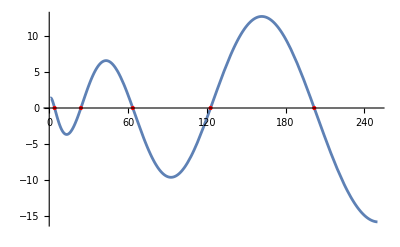

```mathematica
Plot[√λ Cos[√λ]+Sin[√λ], {λ, 1,250}, Epilog->{PointSize[Large], Red, Point[data]}]
```

```mathematica
eigfuns2=Table[y2[x]/. sol2[[1]],{i,5}]
eigvals = List[roots[[All,1,2]]]
```

{Piecewise[{{C[1] (√λ Cos[x √λ]+Sin[x √λ]), √λ Cos[√λ]+Sin[√λ]==0}, {0, True}}],Piecewise[{{C[1] (√λ Cos[x √λ]+Sin[x √λ]), √λ Cos[√λ]+Sin[√λ]==0}, {0, True}}],Piecewise[{{C[1] (√λ Cos[x √λ]+Sin[x √λ]), √λ Cos[√λ]+Sin[√λ]==0}, {0, True}}],Piecewise[{{C[1] (√λ Cos[x √λ]+Sin[x √λ]), √λ Cos[√λ]+Sin[√λ]==0}, {0, True}}],Piecewise[{{C[1] (√λ Cos[x √λ]+Sin[x √λ]), √λ Cos[√λ]+Sin[√λ]==0}, {0, True}}]}

{{4.1158583656945228373,24.139342030445556788,63.659106550438686634,122.88916176192054582,201.85125830031131867}}

Тогда подставим найденные выше значения λ и получим множество собственных функций :

```mathematica
eigfunsfin = Evaluate[eigfuns2/.λ-> eigvals[[1,All]]/.C[1]->1];
```

Определение ортогональности собственных функций проведем аналогично п .1 :

```mathematica
M2=Table[Integrate[eigfunsfin[[1,1,1,1,i]]*eigfunsfin[[1,1,1,1,j]],{x,0,1}],{i,1,Length[eigfunsfin]},{j,1,Length[eigfunsfin]}];
```

```mathematica
M2//MatrixForm
```

(3.057929182847261419 | 0. | 0. | 0. | 0.
0. | 13.06967101522277839 | 0. | 0. | 0.
0. | 0. | 32.82955327521934332 | 0. | 0.
0. | 0. | 0. | 62.44458088096027291 | -6.×10^-19
0. | 0. | 0. | -6.×10^-19 | 101.9256291501556593)

Вывод2 : здесь функции так же обладают свойством ортогональности, соответственно матрице.

Зарисуем графики полученных функций :

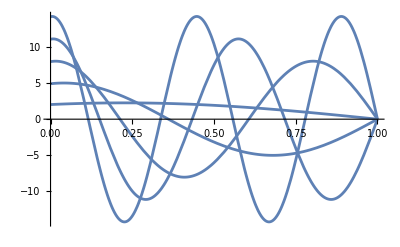

```mathematica
Plot[eigfunsfin[[1,1,1,1,All]],{x,0,1}]
```

Задача 3 : рабочий пример задачи Ш - Л ДУ, приводящий к специальным функциям
Здесь будем решать уравнение бесселя с некоторыми граничными условиями :

```mathematica
eqn={r u''[r]+u'[r]+λ r u[r]==0, u[1]+u'[1]==0};
(*Общее решение*)
sol3=DSolveValue[eqn,u[r],r ]
```

(-BesselJ[0,r √λ] BesselY[0,√λ] C[1]+BesselJ[0,√λ] BesselY[0,r √λ] C[1]-√λ BesselJ[1,√λ] BesselY[0,r √λ] C[1]+√λ BesselJ[0,r √λ] BesselY[1,√λ] C[1])/(-BesselY[0,√λ]+√λ BesselY[1,√λ])

Ожидаемо решение и собственные функции получили в виде Бесселей 1 и 2 рода

```mathematica
roots3 = N[λ /. Solve[sol3[[1,1,2]]==0 && 1< λ < 250, λ]]
```

{4.82743,29.4814,73.8913,138.043,221.934}

```mathematica
eigfuns3 = (sol3/.{C[1]->1})
```

(-BesselJ[0,r √λ] BesselY[0,√λ]+BesselJ[0,√λ] BesselY[0,r √λ]-√λ BesselJ[1,√λ] BesselY[0,r √λ]+√λ BesselJ[0,r √λ] BesselY[1,√λ])/(-BesselY[0,√λ]+√λ BesselY[1,√λ])

```mathematica
eigfunsfin3 = Evaluate[eigfuns3/.λ-> roots3[[All]]/.C[1]->1];
```

```mathematica
eigfunsfin3
```

{-1.92017 (-0.520786 BesselJ[0,2.19714 r]-1.11047 BesselY[0,2.19714 r]),2.93843 (0.340318 BesselJ[0,5.42968 r]+1.83969 BesselY[0,5.42968 r]),-3.68379 (-0.27146 BesselJ[0,8.59601 r]-2.32946 BesselY[0,8.59601 r]),4.30178 (0.232462 BesselJ[0,11.7492 r]+2.72873 BesselY[0,11.7492 r]),-4.84151 (-0.206547 BesselJ[0,14.8974 r]-3.07528 BesselY[0,14.8974 r])}

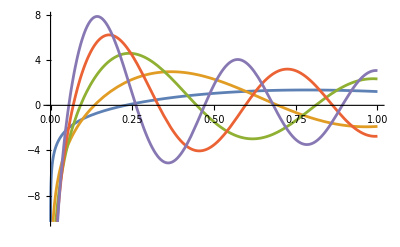

```mathematica
Plot[eigfunsfin3, {r,0,1}]
```

Вывод : были получены навыки решения ШЛ ДУ для различных условий Штурма, была показана ортогональность их решений.